## Визуализация результатов Лабораторной работы №1

### 1. Маятник

```mathematica
Clear["Global`*"];
```

```mathematica
(* Модуль для отрисоввки графиков теста 0 (маятник)*)
TEST0[solve_, data_, text_ : " ", ifhplot_ : False]  := Module[{plotsolve1, plot1data1,plot2data1, ploterror1,plot1, plot2, plot3},
plotsolve1= Plot[solve,{t,0,10},PlotStyle->{Red,Dashed}];

plot1data1= ListPlot[Table[{data[[i]][[1]],data[[i]][[2]]},{i,1,Length[data]}],Joined->True];

plot2data1=ListPlot[Table[{data[[i]][[2]],data[[i]][[3]]},{i,1,Length[data]}],Joined->True,AxesLabel->{"u1", "u2"}];

ploterror1 = ListPlot[Table[{data[[i]][[1]], Abs[(solve/.t->data[[i]][[1]])-data[[i]][[2]]]}, {i,1,Length[data]}], Joined->True,AxesLabel->{"t", "ERROR"}];
Print[text];
plot1 = Show[plot1data1, Graphics[{Red,PointSize[0.01],Point[{data[[1]][[1]],data[[1]][[2]]}]}],plotsolve1,AxesLabel->{"t", "u"},AxesStyle->Arrowheads[0.03], PlotLabel -> "1) Сравнение численного решения с аналитическим",LabelStyle -> Below,ImageSize->400];
plot2 = Show[ploterror1, Graphics[{Red,PointSize[0.01],Point[{data[[1]][[1]],data[[1]][[2]]}]}],AxesLabel->{"t", "Error"},AxesStyle->Arrowheads[0.03], PlotLabel-> "2) График ошибки",ImageSize->400];

plot3 = Show[plot2data1,Graphics[{Red,PointSize[0.01],Point[{data[[1]][[2]],data[[1]][[3]]}]}], AxesStyle->Arrowheads[0.03], PlotLabel-> "3)Фазовая кривая", ImageSize->400];
If[ifhplot, Show[ListPlot[Table[{data[[i]][[1]], Abs[data[[i]][[1]]-data[[i+1]][[1]]]}, {i,1,Length[data]-1}], Joined->True,AxesLabel->{"t", "h"}]]]
plot1
plot2
plot3

(*Show[GraphicsRow[{plot1, plot2, plot3}, ImageSize->1000,Spacings->{0,0}], PlotLabel->text, LabelStyle->"Subsection"]*)

];

(* Заданные условия *)
m = 1; k = 1; 
u10=0;u20=1;
solve1 = DSolve[{y''[t]+k/m y[t]==0,y[0]==u10,y'[0]==u20},y[t],t][[1]][[1]][[2]];
data1=Import["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Численные методы\\Лабораторные работы\\numerical_methods\\Semester_2\\Code_lab_1\\data\\data1.txt","Table"];
data2=Import["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Численные методы\\Лабораторные работы\\numerical_methods\\Semester_2\\Code_lab_1\\data\\data2.txt","Table"];
data3=Import["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Численные методы\\Лабораторные работы\\numerical_methods\\Semester_2\\Code_lab_1\\data\\data3.txt","Table"];
data4=Import["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Численные методы\\Лабораторные работы\\numerical_methods\\Semester_2\\Code_lab_1\\data\\data4.txt","Table"];
data4auto=Import["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Численные методы\\Лабораторные работы\\numerical_methods\\Semester_2\\Code_lab_1\\data\\data4_auto.txt","Table"];
data5=Import["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Численные методы\\Лабораторные работы\\numerical_methods\\Semester_2\\Code_lab_1\\data\\data5.txt","Table"];
data5auto=Import["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Численные методы\\Лабораторные работы\\numerical_methods\\Semester_2\\Code_lab_1\\data\\data5_auto.txt","Table"];
data6=Import["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Численные методы\\Лабораторные работы\\numerical_methods\\Semester_2\\Code_lab_1\\data\\data6.txt","Table"];
data7=Import["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Численные методы\\Лабораторные работы\\numerical_methods\\Semester_2\\Code_lab_1\\data\\data7.txt","Table"];
```

Метод Эйлера явный

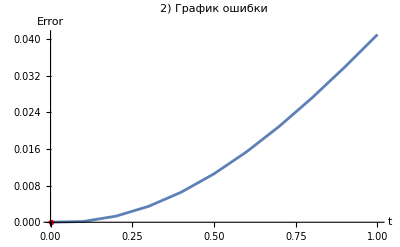
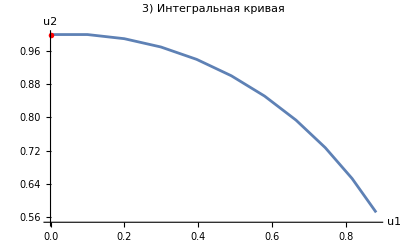
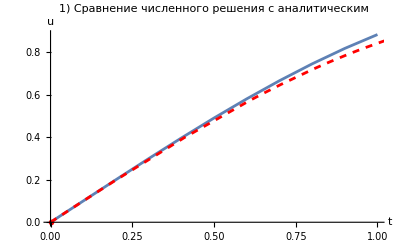
Null -Graphics- -Graphics- -Graphics-

```mathematica
TEST0[solve1, data1, "Метод Эйлера явный"]
```

```mathematica
TEST0[solve1, data2, "Метод Эйлера неявный"]
```

```mathematica
TEST0[solve1, data3, "Симметричная схема"]
```

```mathematica
TEST0[solve1, data4, "Метод Рунге-Кутты 2-х стадийный"]
```

```mathematica
TEST0[solve1, data4auto, "Метод Рунге-Кутты 2-х стадийный c Автоматическим шагом", True]
```

```mathematica
TEST0[solve1, data5, "Метод Рунге-Кутты 4-х стадийный"]
```

```mathematica
TEST0[solve1, data5auto, "Метод Рунге-Кутты 4-х стадийный с Автоматическим шагом", True]
```

```mathematica
TEST0[solve1, data6, "Метод Адамса"]
```

```mathematica
TEST0[solve1, data7, "Метод Прогноз Коррекция"]
```